```mathematica
Integrate[1/(x/c+1)^2,x]
```

-c^2/(c+x)

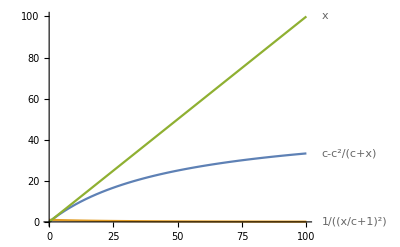

```mathematica
Block[{c=50},Plot[{c-c^2/(c+x),1/(x/c +1)^2,x},{x,0,100},PlotLabels->"Expressions"]]
```

```mathematica
Limit[c-c^2/(c+x),x->Infinity]
```

c

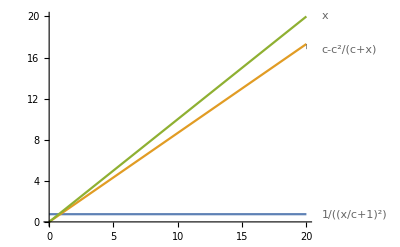

```mathematica
Block[{k = 3/4,c=x/(Sqrt[1/k]-1)},Plot[{1/((x/c)+1)^2,c-c^2/(c+x),x},{x,0,20},PlotLabels->"Expressions"]]
```

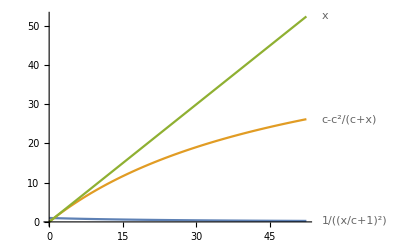
{-Graphics-,52.3861,4.56435}

```mathematica
Block[{b = 5, k = 5/6,c=b/(Sqrt[1/k]-1)},{Plot[{1/((x/c)+1)^2,c-c^2/(c+x),x},{x,0,c},PlotLabels->"Expressions"],N[c],Block[{x=b},N[c-c^2/(c+x)]]}]
```

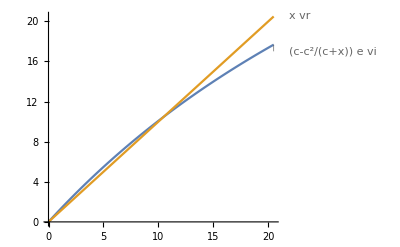
{-Graphics-,{{x→0},{x→10.4772}},52.3861,8.73102}

```mathematica
Block[{vr= 1, vi = 1.0,e=1.2, b = 5, k = 5/6,c=b/(Sqrt[1/k]-1), slv = Solve[(c-c^2/(c+x))*e*vi == x*vr,x]}, {Plot[{(c-c^2/(c+x))*e*vi , x*vr},{x,0,Replace[x,slv[[2]] ] + 10},PlotLabels->"Expressions"],slv, N[c], N[c-c^2/(c+x)/.slv[[2]]]}]
```

```mathematica
Solve[(c-c^2/(c+x))*e*vi == x*vr,x]
```

{{x→0},{x→(c (e vi-vr))/vr}}

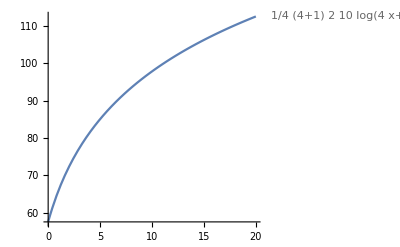
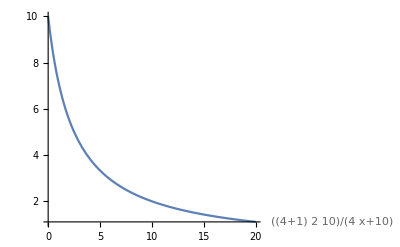

```mathematica
With[{g = 2, s = 10, a = 4}, {Plot[(a+1)/a*g*s*Log[a*x+s],{x,0,2*s}, PlotLabels->"Expressions"],Plot[(a+1)*g*s / (a*x+s),{x,0,2*s}, PlotLabels->"Expressions"]}]
```

```mathematica
D[(a+1)/a*g*s*Log[a*x+s],x]
```

((1+a) g s)/(s+a x)

```mathematica
Block[{s = m, a = 10, x = 2*m},N[((1+a) g s)/(s+a x)]]
```

0.52381 g

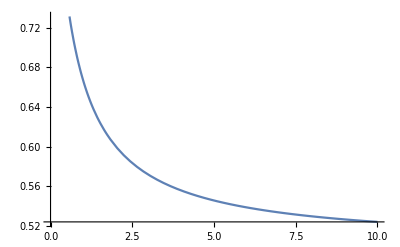

```mathematica
Plot[(1+x)/(1+2x),{x,0,10}]
```

```mathematica
N[Log[2,19]]
```

4.24793

```mathematica
Integrate[2*g*(s^Log[2,19])/(x^Log[2,19] + (s^Log[2,19])),x]
```

2 g x Hypergeometric2F1[1,Log[2]/Log[19],1+Log[2]/Log[19],-s^(-Log[19]/Log[2]) x^(Log[19]/Log[2])]

```mathematica
N[2 g x Hypergeometric2F1[1,Log[2]/Log[19],1+Log[2]/Log[19],-s^(-Log[19]/Log[2]) x^(Log[19]/Log[2])]]
```

2. g x Hypergeometric2F1[0.235409,1.,1.23541,-(1. x^4.24793)/s^4.24793]

```mathematica
Block[{g=2,s=10},N[ g x Hypergeometric2F1[1,Log[2]/Log[19],1+Log[2]/Log[19],-s^(-Log[19]/Log[2]) x^(Log[19]/Log[2])]]]
```

2. x Hypergeometric2F1[0.235409,1.,1.23541,-0.0000565031 x^4.24793]

```mathematica
Integrate[a/(x+b)^n,x]
```

(a (b+x)^(1-n))/(1-n)

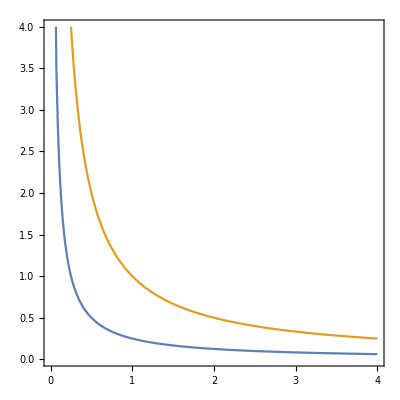

```mathematica
ContourPlot[{1/(2x)==2y,1/(x)==y},{x,0,4},{y,0,4}]
```

```mathematica
N[{b->((-5+(25+88)^(1/2))/2), b->(-5-(25+88)^(1/2))/2}]
```

{b→2.81507,b→-7.81507}

```mathematica
N[{a->1/(2-b)/.#, #}&/@%]
```

{{a→-1.22688,b→2.81507},{a→0.101884,b→-7.81507}}

```mathematica
N[Append[#,n->((1/(1-b))-a)/s/.#]&/@%]
```

{{a→-1.22688,b→2.81507,n→0.675942/s},{a→0.101884,b→-7.81507,n→0.0115579/s}}

```mathematica
Block[{s=10},N[(b+1/(n*x+a)/.#)&@%]]
```

{2.81507+1/(-1.22688+0.0675942 x),-7.81507+1/(0.101884+0.00115579 x)}

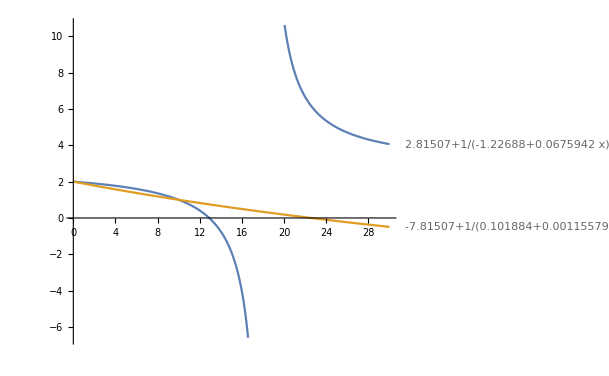

```mathematica
Plot[{2.815072906367325+1/(-1.2268841132959152+0.06759420566479575 x),-7.815072906367325+1/(0.10188411329591558+0.0011557943352042202 x)},{x,0,30},PlotLabels->"Expressions"]
```

```mathematica
Solve[1/(a*Log[b]+c)==2,c]
```

{{c→1/2 (1-2 a Log[b])}}

```mathematica
Solve[1/(a*Log[s+b]+(1/2 (1-2 a Log[b])))==1,b]
```

{{b→s/(-1+ⅇ^(1/2/a))}}

```mathematica
N[Solve[1/(a*Log[2s+(s/(-1+ⅇ^(1/2/a)))]+(1/2 (1-2 a Log[s/(-1+ⅇ^(1/2/a))])))==1/8,a]]
```

{{a→-0.721379},{a→6.51954},{a→0.0133954+0.361762 ⅈ},{a→0.0133954-0.361762 ⅈ},{a→0.0180403+0.378276 ⅈ},{a→0.0180403-0.378276 ⅈ},{a→0.0198242+0.535042 ⅈ},{a→0.0198242-0.535042 ⅈ},{a→0.0455498+0.565588 ⅈ},{a→0.0455498-0.565588 ⅈ},{a→0.0301179+1.04927 ⅈ},{a→0.0301179-1.04927 ⅈ},{a→0.189653+1.10659 ⅈ},{a→0.189653-1.10659 ⅈ}}

```mathematica
Integrate[1/(x^2+b*x+c),x]
```

(2 ArcTan[(b+2 x)/(√(-b^2+4 c))])/(√(-b^2+4 c))

```mathematica
Solve[g==(a (-2 √b+2 √(b+s)))/s,a]
```

{{a→(g s)/(2 (-√b+√(b+s)))}}

```mathematica
Block[{a=(g s)/(2 (-√b+√(b+s)))},Solve[a/(s+b)^(1/2)==g/2,b]]
```

{{b→0}}

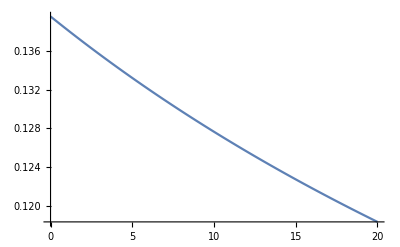
{1849/36,2/15,-Graphics-}

```mathematica
Block[{g=3,a=1,s=10,b=((4 a^2-g^2 s)^2)/(16 a^2 g^2)},{b,(a (-2 √b+2 √(b+s)))/s,Plot[a/(x+b)^(1/2),{x,0,20}]}]
```

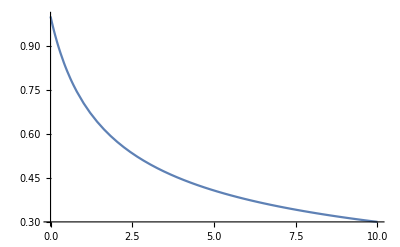

```mathematica
Plot[1/(x+1)^(1/2),{x,0,10}]
```

```mathematica
Integrate[x^a*(1-x)^y,x]
```

(x^(1+a) Hypergeometric2F1[1+a,-y,2+a,x])/(1+a)

```mathematica
D[(x^(1+a) Hypergeometric2F1[1+a,-y,2+a,x])/(1+a),x]
```

x^a ((1-x)^y-Hypergeometric2F1[1+a,-y,2+a,x])+x^a Hypergeometric2F1[1+a,-y,2+a,x]

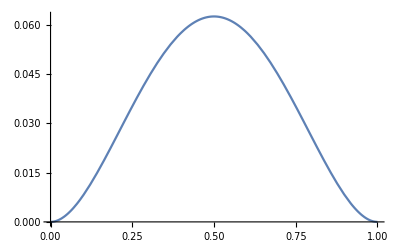

```mathematica
Block[{a=2,y=2},Plot[x^a ((1-x)^y-Hypergeometric2F1[1+a,-y,2+a,x])+x^a Hypergeometric2F1[1+a,-y,2+a,x],{x,0,1}]]
```

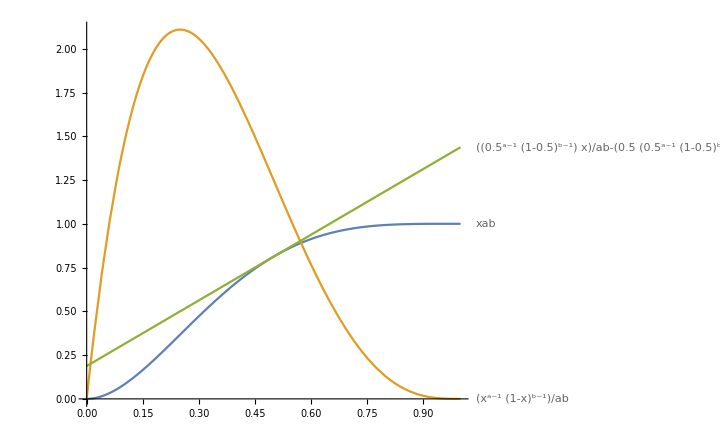

```mathematica
Block[{a=2,b=4},Plot[{BetaRegularized[x,a,b],
(x^(a-1)*(1-x)^(b-1))/Beta[a,b],
(((0.5)^(a-1)*(1-0.5)^(b-1))/Beta[a,b])*x-(0.5)*(((0.5)^(a-1)*(1-0.5)^(b-1))/Beta[a,b]) + BetaRegularized[0.5,a,b]},{x,0,1},PlotLabels->"Expressions"]]
```

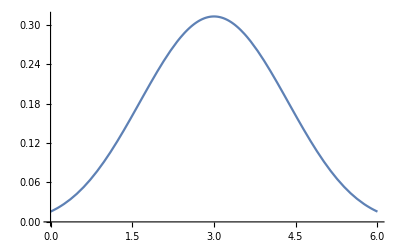

```mathematica
Block[{c=0.5,b=6},Plot[Gamma[b+1]*c^a*(1-c)^(b-a)/(Gamma[a+1]*Gamma[b-a+1]),{a,0,6}]]
```

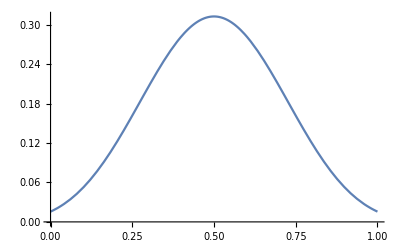

```mathematica
Block[{c=0.5,b=6},Plot[Gamma[b+1]*c^(a*b)*(1-c)^(b-a*b)/(Gamma[(a*b)+1]*Gamma[b-(a*b)+1]),{a,0,1}]]
```

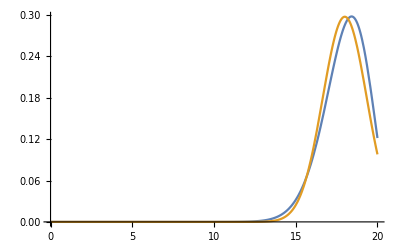

```mathematica
Block[{c=0.9,b=20,al =x+1, bl =b-x+1},Plot[{c^(x)*(1-c)^(b-x)/((b-x)*Beta[x+1,b-x]),
1/(2*b*c*(1-c)*π)^(1/2)*E^(-(x-b*c)^2/(2*b*c*(1-c)))},{x,0,b}]]
```

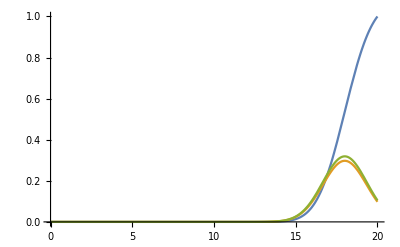

```mathematica
Block[{c=.9,b=20, d=(2*b*c*(1-c))^(1/2)},Plot[{
(Erf[(x-b*c)/d]-Erf[-b*c/d])/(Erf[(b-b*c)/d]-Erf[-b*c/d]),
1/(2*b*c*(1-c)*π)^(1/2)*E^(-(x-b*c)^2/(2*b*c*(1-c))),
E^-(((x-b*c)/d)^2)*2/((π)^(1/2)*d*(Erf[(b-b*c)/d]-Erf[-b*c/d]))},{x,0,b},PlotRange->Full]]
```

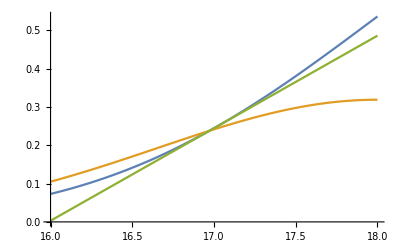

```mathematica
Block[{c=.9,b=20, d=(2*b*c*(1-c))^(1/2)},Plot[{
(Erf[(x-b*c)/d]-Erf[-b*c/d])/(Erf[(b-b*c)/d]-Erf[-b*c/d]),
E^-(((x-b*c)/d)^2)*2/((π)^(1/2)*d*(Erf[(b-b*c)/d]-Erf[-b*c/d])),
x*(E^-(((17-b*c)/d)^2)*2/((π)^(1/2)*d*(Erf[(b-b*c)/d]-Erf[-b*c/d])))-17*(E^-(((17-b*c)/d)^2)*2/((π)^(1/2)*d*(Erf[(b-b*c)/d]-Erf[-b*c/d])))+(Erf[(17-b*c)/d]-Erf[-b*c/d])/(Erf[(b-b*c)/d]-Erf[-b*c/d])},{x,16,18}]]
```

```mathematica
Block[{d=d=(2*b*c*(1-c))^(1/2)},D[(Erf[(x-b*c)/d]-Erf[-b*c/d])/(Erf[(b-b*c)/d]-Erf[-b*c/d]),x]]
```

(ⅇ^(-(-b c+x)^2/(2 b (1-c) c)) √(2/π))/(√(b (1-c) c) (Erf[(b c)/(√2 √(b (1-c) c))]+Erf[(b-b c)/(√2 √(b (1-c) c))]))